This Notebook imports .dat files (for local Chern number on every site of a square lattice), and picks out the sites which are on the straight line parallel to the x axis, going through the midpoint of the lattice (i.e., the line given by the equation y = Ly/2, where Ly is the number of lattice sites along the y direction). Then it plots the local Chern number on every site.

The dat files imported in this notebook are generated by Local_Chern_Number_QAHI.nb

```mathematica
Lx = 60;
Ly = 60;
```

```mathematica
(** Here we import the dat files **)
```

```mathematica
LineChernListP1 = Import["data/datalocalChernLx=60Ly=60m=6.dat"];
```

```mathematica
LineChernListP2  = Import["data/datalocalChernLx=60Ly=60m=2.dat"];
```

```mathematica
(** We generate the indices of the sites of the line y = Ly/2, and store them in a list **)
```

```mathematica
SiteIndexList = Table[(Round[Ly/2]-1)*Lx + ii,{ii,1,Lx} ];
```

```mathematica
(** We isolate the local Chern number on the sites on the line y = Ly/2 **)
```

```mathematica
list1 = Table[LineChernListP1[[SiteIndexList[[ii]]]][[1]],{ii,1,Lx}]
```

{-25.6348,-0.0653543,-0.959296,0.877681,0.818942,0.985207,0.981911,0.998127,0.998095,0.999754,0.99979,0.999966,0.999976,0.999995,0.999997,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999997,0.999995,0.999976,0.999966,0.99979,0.999754,0.998095,0.998127,0.981911,0.985207,0.818942,0.877681,-0.959296,-0.0653543,-25.6348}

```mathematica
list2 = Table[LineChernListP2[[SiteIndexList[[ii]]]][[1]],{ii,1,Lx}]
```

{25.6348,0.0653543,0.959296,-0.877681,-0.818942,-0.985207,-0.981911,-0.998127,-0.998095,-0.999754,-0.99979,-0.999966,-0.999976,-0.999995,-0.999997,-0.999999,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-0.999999,-0.999997,-0.999995,-0.999976,-0.999966,-0.99979,-0.999754,-0.998095,-0.998127,-0.981911,-0.985207,-0.818942,-0.877681,0.959296,0.0653543,25.6348}

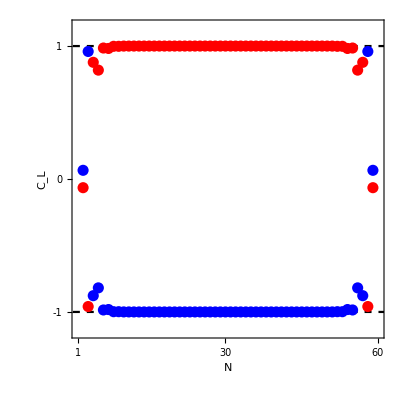

```mathematica
Show[Plot[1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.15,1.15}},Frame->True,Axes->False],
Plot[-1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.15,1.15}},Frame->True,Axes->False],
ListPlot[list1,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Red,PointSize[0.02]},Axes->False],
ListPlot[list2,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 24,
FrameTicks->{ {{{-1,"-1"},{0,"0"},{1,"1"}},None},{{1,Lx/2,Lx},None}},
ImageSize-> 400,AspectRatio-> 1,
FrameLabel->{"N","C_L"},RotateLabel->False]
```